# Lab 7

## Victoire Djuidje

March 13 2023

```mathematica
Remove["Global`*"]
```

Part one: ContourPlot the function then form 2D vector field and plot field on top of contour plot. Then calculate gradient.

```mathematica
f= y *((Exp[-x]+1) / (Exp[-x]+3))
```

((1+ⅇ^-x) y)/(3+ⅇ^-x)

Plot with no shading and contours labeled

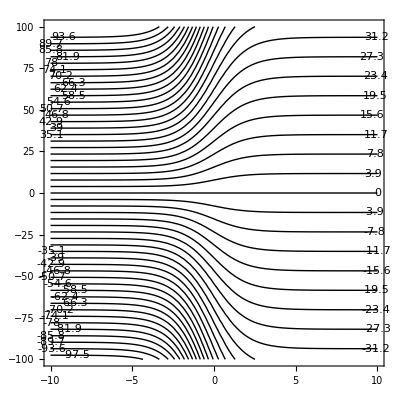

```mathematica
P1=ContourPlot[f, {x,-10,10},{y,-100,100}, PlotRange->All, Contours->50, ContourShading->None, ContourLabels->True]
```

Plot of function with no contour labels

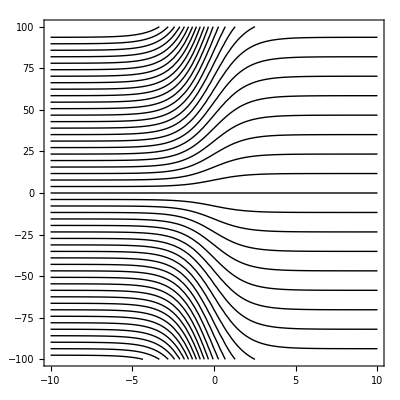

```mathematica
P1a=ContourPlot[f, {x,-10,10},{y,-100,100}, PlotRange->All, Contours->50, ContourShading->None]
```

Plot with shading and no contour labels

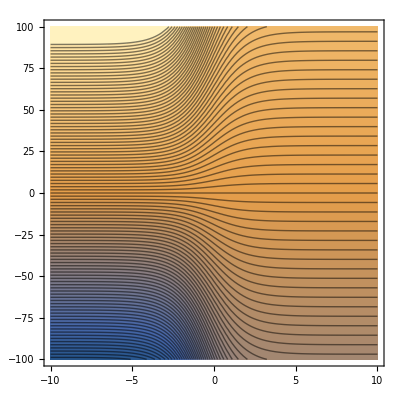

```mathematica
P2=ContourPlot[f, {x,-10,10},{y,-100,100}, PlotRange->All, Contours->100, ContourShading->True]
```

2D vector field (x,y) of the function plus its plot on top of P1.

```mathematica
v = Grad[f,{x,y}]
```

{(ⅇ^-x (1+ⅇ^-x) y)/((3+ⅇ^-x)^2)-(ⅇ^-x y)/(3+ⅇ^-x),(1+ⅇ^-x)/(3+ⅇ^-x)}

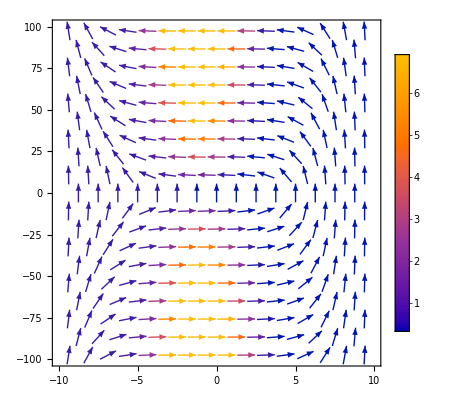

```mathematica
P3=VectorPlot[v,{x,-10,10},{y,-100,100},PlotLegends->Automatic]
```

Combination of plot of original function and plot of vector field

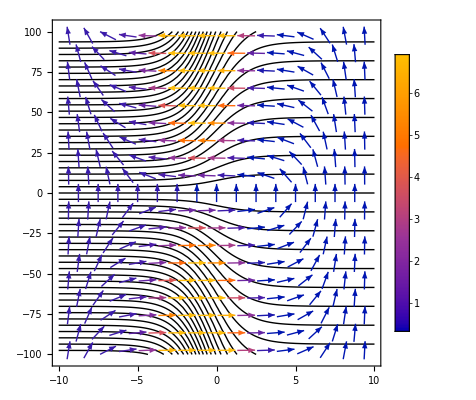

```mathematica
Show[P1a,P3]
```

Converting 2D vector field to 3D

```mathematica
v1 = Grad[f,{x,y,z}]
```

{(ⅇ^-x (1+ⅇ^-x) y)/((3+ⅇ^-x)^2)-(ⅇ^-x y)/(3+ⅇ^-x),(1+ⅇ^-x)/(3+ⅇ^-x),0}

```mathematica
VectorPlot3D[v1,{x,-10,10},{y,-100,100},{z,-10,10},VectorMarkers->"Arrow"]
```

-Graphics3D-

```mathematica
Curl[v1,{x,y,z}]
```

{0,0,0}

This makes sense because the curl of a gradient is always zero.

Part Two: Construct vector plot of the field then find curl and make a contour plot of curl with vector plot. Then find divergence of curl

```mathematica
v2 = {-y*r,x*r}
r = Sqrt[x^2 + y^2]
```

{-r y,r x}

√(x^2+y^2)

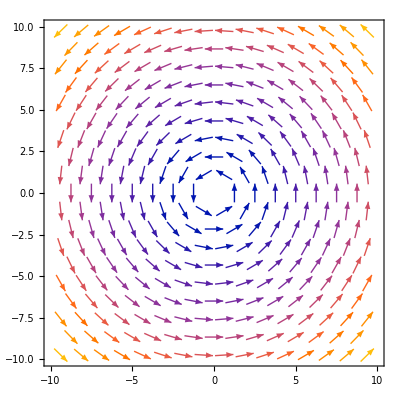

```mathematica
Pv=VectorPlot[v2, {x,-10,10},{y,-10,10}]
```

```mathematica
w=Curl[v2,{x,y}]
```

x^2/(√(x^2+y^2))+y^2/(√(x^2+y^2))+2 √(x^2+y^2)

w has to point in the

```mathematica
magw = Norm[w]
```

Norm[x^2/(√(x^2+y^2))+y^2/(√(x^2+y^2))+2 √(x^2+y^2)]

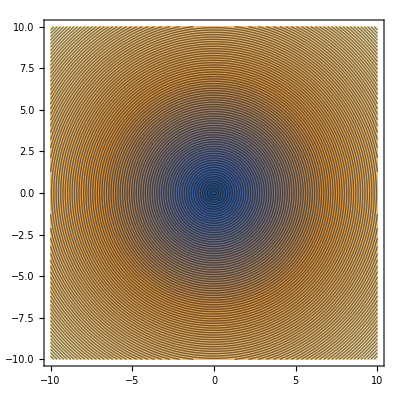

```mathematica
Pws=ContourPlot[magw,{x,-10,10},{y,-10,10}, Contours->100]
```

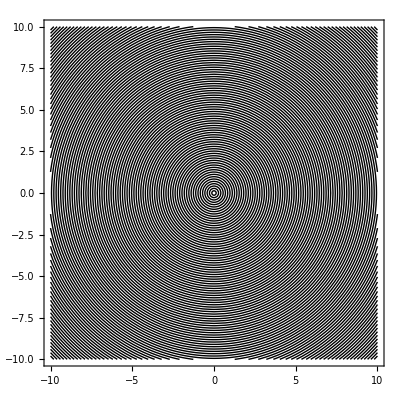

```mathematica
Pw=ContourPlot[magw,{x,-10,10},{y,-10,10}, Contours->100, ContourShading->None]
```

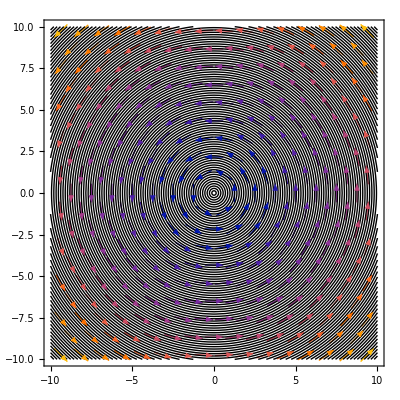

```mathematica
Show[Pv,Pw]
```

```mathematica
Grad[w,{x,y}]
```

{-x^3/((x^2+y^2)^(3/2))-(x y^2)/((x^2+y^2)^(3/2))+(4 x)/(√(x^2+y^2)),-(x^2 y)/((x^2+y^2)^(3/2))-y^3/((x^2+y^2)^(3/2))+(4 y)/(√(x^2+y^2))}

Part Three: Plot vector field then find curl

```mathematica
v3 = {-y/r^2, x/r^2}
```

{-y/(x^2+y^2),x/(x^2+y^2)}

```mathematica
w1=Curl[v3,{x,y}]
```

-(2 x^2)/((x^2+y^2)^2)-(2 y^2)/((x^2+y^2)^2)+2/(x^2+y^2)

```mathematica
Simplify[w1]
```

0